```mathematica
(*David Stuart:Measure mass of blue BBs*)

(* First we need the error bar plotting package *)
Needs["ErrorBarPlots`"];
```

```mathematica
n={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50};

m={26.33,26.44,26.56,26.66,26.77,26.88,26.98,27.09,27.20,27.31,27.42,27.53,27.64,27.74,27.86,27.96,28.06,28.18,28.29,28.38,28.49,28.60,28.72,28.82,28.93,29.05,29.15,29.25,29.36,29.48,29.57,29.68,29.78,29.89,29.99,30.10,30.22,30.33,30.43,30.54,30.65,30.75,30.86,30.97,31.08,31.19,31.30,31.42,31.52,31.63};

dm={0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000,0.007000};
```

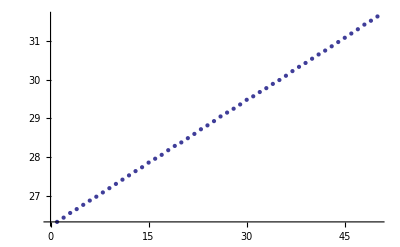

```mathematica
(* Graph m vs n 
This is done by making a table (~ an array) of m and m. 
The {i, 1, Length[n]} implies a loop over i.
Then, a simple ListPlot command makes a quick graph.
*)
mVn = Table[ {n[[i]],m[[i]]},{i,1,Length[n]} ];
ListPlot[mVn]
```

```mathematica
(* 
Graph m vs n with dm as the error bar.
Again we make a table but now there are two brackets "{" in the table so the ErrorBar piece comes in as the second element.
*)
mVnErr = Table[ {   {n[[i]],m[[i]]},ErrorBar[dm[[i]]] },{i,1,Length[n]} ];
ErrorListPlot[mVnErr]
```

-Graphics-

```mathematica
(* The error bars are too small to see, but it is important to have them there in order to do a fit. *)
```

```mathematica
(* 
We can do a fit in two ways either a simple linear fit or a fit to a more complicated model. We'll do both. 
*)
```

```mathematica
(* A simple linear fit that ignores uncertainties i.e. treats them all as being just unity. *)
mVnSimpleFit = Fit[mVn, {1,x}, x]
```

26.2317+0.107799 x

```mathematica
(* Now do a more sophisticated fit that includes the uncertainties. Here we will use the NonLinearModelFit which can take any functional form. But we will just give it a line as the function. *)
mVnLinearFit = NonlinearModelFit[mVn,intercept+slope*x, {{intercept,1.},{slope,2.}},x,Weights-> 1/dm^2]
```

FittedModel[26.2317+0.107799 x]

```mathematica
(* That gives the same fit values which is not surprising because all points have the same uncertainty. In that case the size of the uncertainty on the points only affects the uncertainty on the fitted values not the values themselves. Now we will look at the fitted values AND their uncertainties. *)
mVnLinearFit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
intercept | 26.2317 | 0.00202211 | 12972.5 | 9.63339×10^-159
slope | 0.107799 | 0.0000690136 | 1561.99 | 1.29431×10^-114

```mathematica
(* Now lets calcualte the residuals. There is a built in function for this which is mVnLinearFit["FitResiduals"] but that doesnt give the uncertainties. So we will calculate them directoy with a subtraction and pass the errorbars. Then we will plot them. *)

residVn =Table[{{n[[i]],mVn[[i,2]] - mVnLinearFit[mVn[[i,1]]]},ErrorBar[dm[[i]]]},{i,1,Length[n]}];
```

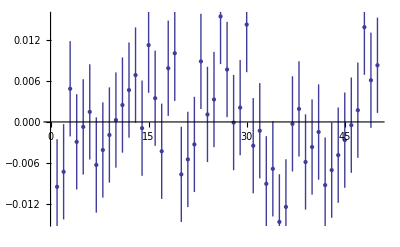

```mathematica
ErrorListPlot[residVn]
```

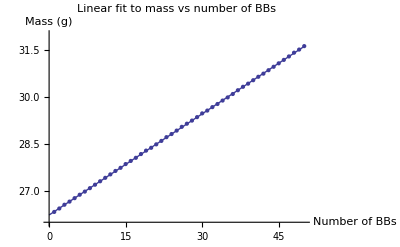

```mathematica
(* Finally lets make cleanly labeled versions of the plots *)
Show[
Plot[mVnLinearFit[x], {x, 0, 50}, 
PlotLabel-> "Linear fit to mass vs number of BBs", 
AxesLabel->{"Number of BBs","Mass (g)"},
PlotRange->{26.,32.}],
ErrorListPlot[mVnErr]
]
```

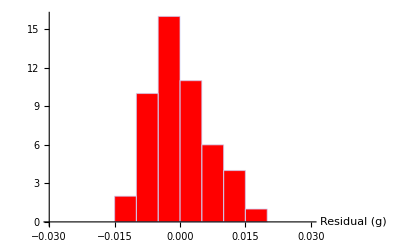

```mathematica
(* Make a histogram of the residuals to see if they distribute as expected. *)
Residuals = mVnLinearFit["FitResiduals"];
Histogram[Residuals,{-0.03,0.03,0.005},
AxesLabel->{"Residual (g)"," "},
AxesOrigin->{-0.03,0},
ChartStyle->Red]
```

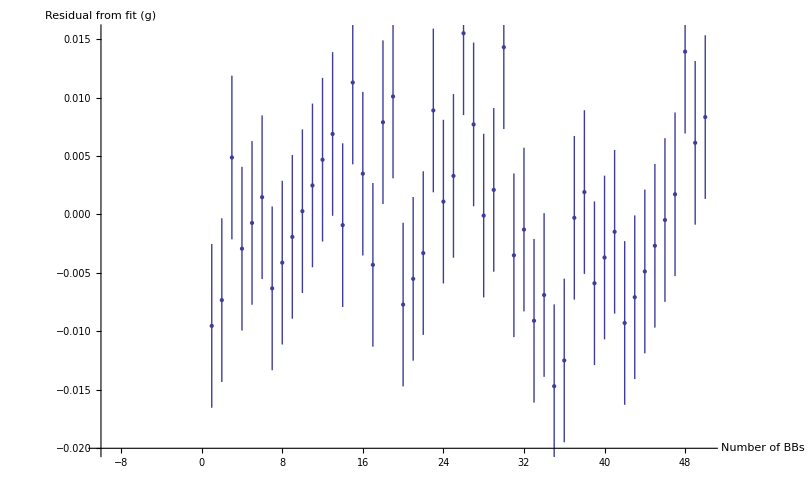

```mathematica
(* The saw-tooth pattern in the plot of residual vs number of BBs is interesting and worth recording in a well formatted plot. So we do that here. *)
ErrorListPlot[residVn,
BaseStyle->{FontSize->16},
AxesLabel->{"Number of BBs","Residual from fit (g)"},
AxesOrigin->{-10,-0.02}]
```

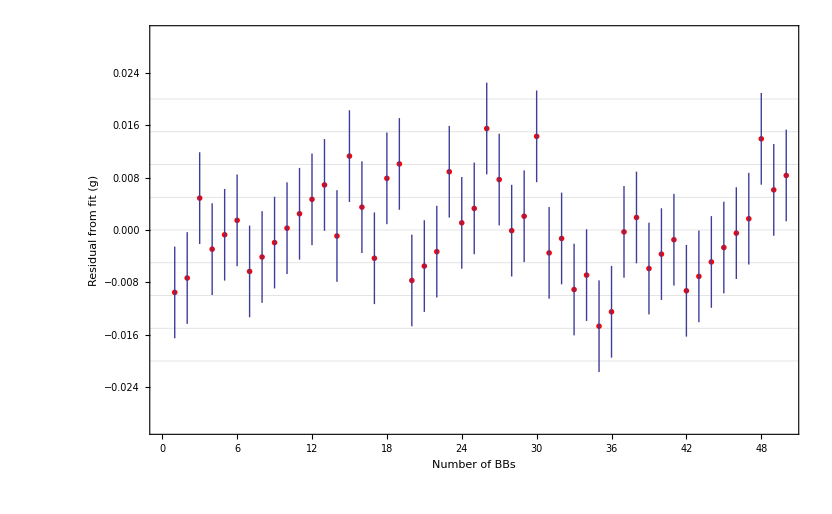

```mathematica
(* If you want to put the axis labels on the sides rather than the ends of the axes then call them "Frame" labels as shown below. And we also draw some grid lines to guide the eye. *)
marker1 = Graphics[{Red,Disk[]}];
ErrorListPlot[residVn,
BaseStyle->{FontSize->18},
Frame->{True,True,False,False},FrameLabel->{"Number of BBs","Residual from fit (g)"},
GridLines->{{},{0, 0.005, -0.005, 0.01, -0.01, -0.015, 0.015,-0.02, 0.02}},
PlotRange-> {-0.03,0.03},
PlotMarkers-> {marker1,0.02},(* 0.02 specifies the marker size *)
AxesOrigin->{0,-0.03}]
```